Last modified on: Tuesday, July 10, 2018 at 17:16

Author Info

Lawrence Temlock

Carl Woll

The Sun Exchange

Poster Session Content

Computing Text Reading Levels

Train a neural network to recognize text reading level

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

Classical readability indices use counts of words, syllables, and word frequencies.  Recent systems such as Lexile leverage reading research and psychometric theory to score and match readers and books.   Text context, subject matter and other subtle characteristics don’t generally factor into readability indices commonly used in education, state policy, the military, and the media. 

In this project, three approaches were used to test if a neural network can be trained to generate meaningful readability scores.  97,000 text samples, 50-500 characters long, were collected and targeted with Lexile L-scores ranging from 430L (elementary) to 1350L (high school).  

In Trial 1, text data was assigned 100-column feature vectors from a GloVe net model*, and input to a network embedding layer. Trial 2 input a 1-column word frequency vector; Trial 3 combined these two elements with NetEncoding. The common network architecture assembled two gated recurrent layers, followed by a sequence last layer and a linear layer.  

The three network training trials were unable to produce networks capable of meaningfully scoring text reading level.  The result of Trial 1 was overfitting.  Trials 2 and 3 both failed to reduce the output from the loss function. Random sample results from the networks compared unfavorably with those generated by the Dale-Challs Raw Score and Automated Readability Index.

(1) Remove unrepresentative text from data, (2) use alternative, more accurate scoring on a sample-by-sample basis, (3) diversify subject matter and level, (4) train nets longer, (5)  alternative model to GloVe Feature, (6) input sentence structure, parts of speech, (6) test with more network layers

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

The project generally suffered from a data quality issue.  Most significantly, the book title for each text sample was used to look up a Lexile L-score at https://fab.lexile.com/.   It was not possible to assign a Lexile score based on the content of each text sample; scoring was done on a book title level.  This probably resulted in lower correlation between Lexile scores and text reading difficulty levels, and made it difficult to train the neural networks.  Although a free Lexile text analyzer was available at https://la-tools.lexile.com/free-analyze/, it was not possible to automate the text scoring process for the text samples in the time available.  For future tests, individual text scoring should be implemented.

* GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data (“GloVe Feature”)

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Abstract

Classical readability indices use counts of words, syllables, and word frequencies.  Recent systems such as Lexile leverage reading research and psychometric theory to score and match readers and books.   Text context, subject matter and other subtle characteristics don’t generally factor into readability indices commonly used in education, state policy, the military, and the media.  In this project, three approaches were used to test if a neural network can be trained to generate meaningful readability scores.  97,000 text samples, 50-500 characters long, were collected and targeted with Lexile L-scores ranging from 430L (elementary) to 1350L (high school).  In Trial 1, text data was assigned 100-column feature vectors from a GloVe net model*, and input to a network embedding layer. Trial 2 input a 1-column word frequency vector; Trial 3 combined these two elements with NetEncoding. The common network architecture assembled two gated recurrent layers, followed by a sequence last layer and a linear layer.  The three network training trials were unable to produce networks capable of meaningfully scoring text reading level.  The result of Trial 1 was overfitting.  Trials 2 and 3 both failed to reduce the output from the loss function. Random sample results from the networks compared unfavorably with those generated by the Dale-Challs Raw Score and Automated Readability Index.

#### Background

Many scientific readability indices have been developed to determine the reading levels of texts since the late 1940’s. Indices based on ratios of word counts and syllables, ratios of ‘easy’ words to total words used, and other textual characteristics dominate in these approaches.  Popular indices such as the Fry Readability Graph, Flesch Reading Ease Test, Dale-Chall Raw Score, SMOG and FOG tests have been widely used for assessments in the military, education, and for various other purposes including state regulation of insurance policies.  

The common structure of most current readability formulas is that it consists of a limited number of parameters that reflect either the reading difficulties on the word level, or on the sentence level. For example, the parameters average sentence length and number of different words are often used. Almost every readability formula consists of parameters that represent either semantic or syntactic complexity. The parameters get a score of how well they correlate with the classified data and then the parameters, or combinations of parameters, with the highest score are used in the formula. The output of a readability formula is usually a classification into the level of education the reader needs to be able to understand the text.

Below are some examples of classical readability tests:

Dale-Chall Raw Score for Reading Level

The original Dale-Chall Formula was developed for adults and children above the 4th grade level, and aimed to correct certain shortcomings in the Flesch Reading Ease Formula. It was a sentence-length variable plus a percentage of hard words— words not found on the Dale-Chall long list of 3000 easy words, 80 percent of which are known to fourth-grade readers.

```mathematica
Clear[ASL,PDW,a,b,c]
a = 0.1579; b = 0.496; c=.6365; 
PDW[text_]:=1-Total[WordFrequency[text,daleChalls3000]]
ASL[text_]:=N[Mean[WordCount/@TextCases[text,"Sentences"]]]
DaleChallRawScore[text_]:=a * PDW[text] +b * ASL[text] + c
```

Automated Readability Index

The Automated Readability Index (ARI) relies on characters per word instead of syllables per word which distinguishes this measurement from many other types of readability measurements. It is easier to calculate accurately since determining the number of characters is easier than determining syllables.

```mathematica
Clear[a,b,c,sentences,wordcounts,characters]
a=4.71;b=0.5;c=21.43;
sentences[text_]:=Length[TextCases[text,"Sentences"]];
wordcounts[text_]:=WordCount[text];
characters[text_] := StringLength[text];
ARI[text_]:=a *characters[text]/wordcounts[text] + b*wordcounts[text]/sentences[text] - c
```

Coleman - Liau Formula

```mathematica
a=5.89;b=0.3;c=15.8;
Coleman[text_]:=a*characters[text]/wordcounts[text] - b*sentences[text]/(100*wordcounts[text])-c
```

#### Limited Utility of Traditional Readability Scores

Many studies have been done on the accuracy of traditional systems for reading level indexation.   One interesting study by Reck & Reck in 2012, “Generating and Rendering Readability Scores for Project Gutenberg Texts”, applying various scoring systems to 15,000 digitized texts.   The results demonstrated that many of the commonly-used scoring systems produced relatively narrow score distributions.  The study also identified that the distribution of counts of syllables per word, words per sentence, and characters per word are narrow in the Gutenberg Project data set, which helps explain the narrow distributions of the readability indices.

Readability Scores For The Gutenberg Project

```mathematica
Grid[{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},Frame->All]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

Distributions of counts of characters/word, words/sentence, and syllables/word

```mathematica
Grid[{{-Graphics-,-Graphics-,-Graphics-}},Frame->All]
```

-Graphics- | -Graphics- | -Graphics-

Additionally, a common characteristic in all methods is that they have been developed for documents with at least 10 sentences or 100 words. Therefore, traditional scoring systems may be unreliable when the size of the text drops below the requirement, as frequently occurs in the current media environment.

New developments in readability scoring systems

A variety of reading indices are currently available on the Internet.  Examples include grade level rankings by Amazon.com and Scholastic.com, Readable.io, the Classroom Library Company, and others.  Increases in computational and research resources have also resulted in several new statistical approaches during the last two decades.  One such approach the Lexile Framework for Reading, based research led by A. Jackson Stenner and Malbert Smith, and funded by U.S. The National Institute of Child Health and Human Development (NICHD). The Lexile framework utilizes quantitative methods, based on individual words and sentence lengths, rather than qualitative analysis of content to produce scores. Accordingly, the scores for texts do not reflect factors such as multiple levels of meaning or maturity of themes.  

In the US, Lexile measures are reported from reading programs and assessments annually; about half of U.S. students in grades 3rd through 12th receive a Lexile measure each year.  In addition to being used in schools in all 50 states, Lexile measures are also used in 24 countries outside of the United States. As with the Amazon.com and other grading systems, the Lexile scoring algorithm has not been publicly disclosed, nor is the distribution of scores among ranked books.   See https://lexile.com/ for additional information.

#### The Data Set

For text inputs to the network, 97,114 text samples ranging from 50 to 500 characters were collected from from 76 books, from websites including The Gutenberg Project, ReadersRead.com, Crossroadsbook.com, and the Wolfram Data Repository.  Text samples were cleaned to remove special characters and carriage returns.  

For target inputs, the book title for each text sample was used to look up a Lexile L-score at https://fab.lexile.com/.   It was not possible to assign a Lexile score based on the content of each text sample; although a free Lexile text analyzer was available at https://la-tools.lexile.com/free-analyze/, it was not possible to automate the text scoring process for the text samples.  This probably resulted in lower correlation between Lexile scores and text reading difficulty levels, and made it difficult to train the neural networks. The Lexile scores were rescaled in the data from {430, 1350} to {-1,1}.

An additional vector of data for each text sample was constructed with word frequencies.  For each word in the text, two types of vectors were created:  
(1) vectors of frequencies based on membership in the “Dale-Challs 3000” simple word list reordered by frequency in English, and 
(2) frequencies in the English language overall.  
For the neural network training trials, only (2), the vector of frequencies in the English language, was used.

Below is histogram of the Lexile rankings of the books in the data set:

Distribution of Lexile L-scores in this data set of 76 books

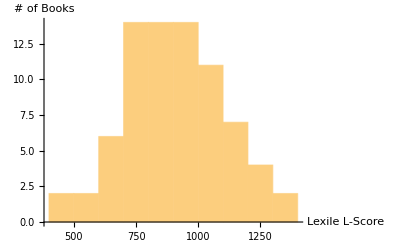

```mathematica
lexileBookList={760,750,720,680,940,730,840,1030,740,970,870,720,1010,820,700,780,760,640,800,830,830,680,970,730,1150,1150,830,900,910,600,840,900,790,650,960,950,980,800,800,430,800,1020,1070,480,1090,1120,730,1210,1050,1160,1210,1350,1060,850,1320,1260,1020,1180,590,1210,960,960,1040,930,880,780,510,1100,690,760,1040,910,1030,1160,970,890};
Histogram[lexileBookList,10,AxesLabel->{"Lexile L-Score","# of Books"}]
```

#### Classification Trial

Initially, classification of text was attempted with the Classify function in the Wolfram Language, on various subsets of the data set. 

The Classify function failed to produce a meaningful function for scoring randomly selected text samples.   As a result, the project progressed to neural net design and training.

#### Net Model Selection

The net model used was the GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data model.  

GloVe is an unsupervised learning algorithm for obtaining vector representations for words; in this case, 100-dimensional vectors. Training is performed on aggregated global word-word co-occurrence statistics from a data set, and the resulting representations showcase linear substructures of the word vector space. Released in 2014 by the computer science department at Stanford University, this representation encodes 400,000 tokens as unique vectors. Token case is ignored.  

For each text sample, the net model produced an n x 100 feature matrix (hereafter, the “GloVe Feature”), with n = the number of words in the text sample. 

The GLoVe Feature code, and an example of creation of a feature matrix, are:

```mathematica
feature=NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"]
```

EmbeddingLayer[<>]

```mathematica
exampleText = "Wolfram Summer School project notebook";
feature[exampleText]//Dimensions
```

{5,100}

#### Network Training Trials

Three types of inputs were used in network training trials.  

Trial 1:  Each text sample with n words created an n x 100 GloVe Feature matrix, for input to the embedding layer of the network. 
Trial 2:  Each text sample with n words created an n x 1 word frequency vector, for input to the first gated recurrent layer of the network.  Each vector element represented the frequency of the text sample word in the English language, based on Wolfram data. 
Trial 3:  A combination of the Trial 1 and Trial 2 data sets.   An n x 101 matrix for input to the first gated recurrent layer of the network.

Trial 1 used the GloVe Feature as the first layer in the network; the set of text samples was input to the network.  
Trails 2 and 3 used NetEncoding to create inputs for the first gated recurring layer in the network.

An example of the data used in Trial 1 is:

Example code for the NetEncoding used is :

```mathematica
enc1 = NetEncoder[{"Function", joinVectors, {"Varying", 1}}]
enc101=NetEncoder[{"Function",joinVectors,{"Varying",101}}]
```

NetEncoder[<>]

NetEncoder[<>]

#### Network Design

The common network architecture assembled two gated recurrent layers, followed by a sequence last layer and a linear layer.  Similar simple designs were used for the three network training trials:

```mathematica
net1=NetChain[{feature,GatedRecurrentLayer[10],GatedRecurrentLayer[10],SequenceLastLayer[],LinearLayer[]},"Output"->"Scalar"];
NetInitialize@net1
```

NetChain[<>]

```mathematica
net2=NetInitialize@NetChain[{GatedRecurrentLayer[10],GatedRecurrentLayer[10],SequenceLastLayer[],LinearLayer[1]},"Input"->enc1,"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
net3=NetInitialize@NetChain[{GatedRecurrentLayer[10],GatedRecurrentLayer[10],SequenceLastLayer[],LinearLayer[1]},"Input"->enc101,"Output"->"Scalar"]
```

NetChain[<>]

#### Net Training Results

In training the networks, learning rate multipliers were set to freeze the first layer.   Data sampling was randomized.  The test/validation set was selected by the NetTrain function as a subset of the data set.

Similar instances of NetTrain were used for all trials.
      train1 = NetTrain[net1, RandomSample[allData, 3000], LearningRateMultipliers -> {1 -> 0, _ -> 1}, 
      MaxTrainingRounds -> 10000, ValidationSet -> Scaled[0.1]]

Trial 1

The result from Trial 1 was an overfit network, as evident from the divergence of the blue and orange lines in the chart below:

-Graphics-

Trial 2

The result from Trial 2 was a network unable to learn from the data set.  After training over 45 minutes,  there was very little improvement in the loss results.

Trial 3

The result from Trial 3 was a network that learned very slowly from the data set.   Were it possible to train the network for a longer time period over a larger data set, greater learning may occur.

#### Conclusions and Future Experimentation

For future experimentation, the following can be considered:

(1) Human checking of the text samples for approximate correlation with target reading level data set is required.
- More accurate Lexile scores relating to individual text passages, not entire books, will likely be better correlated with reading level difficulty, resulting in network training success.
- An alternative to the Lexile scale may produce better results from network training.  Based on the distributions from the Reck & Reck’s Gutenberg Project study, the Flesch index can be considered as an alternative readability measure for the data set.  However, the Flesch system requires counting syllables, which is difficult to implement in computer code.
- Limiting text samples to those from books written after a cutoff year, such as 1975, may provide more consistent samples of vocabulary, grammar, and context for the network to train on
- A data set with greater diversity of reading levels, genre, and subject matter could improve model utility
- Additional data relating to sentence structure in the text samples, for example using the TextStructure function, may help to train networks

(2) Longer text samples may be better suited for creating vectors of word frequency data.   
- According to Zipf’s Law, given a large sample of words used, the frequency of any word is inversely proportional to its rank in the frequency table. Because word number N has a frequency proportional to 1/N, a relatively large sample of words is required to generate measurable frequencies.  
- Empirically, the shape of the distribution of word frequencies in this data set (see chart below), generated from text samples 50-500 characters long, generally seems to support Zipf’s proposition, and demonstrates that low word frequencies were recorded for all but the 50 most frequent words in the Dale 3000 word subset.

(3) Alternatives to the GloVe 100 - D feature model should be considered.  
   - The GloVe model used for this project is designed to describe linear substructures of the word vector space.  It may not be appropriate for learning features of text that provide information about readability, such as vocabulary difficulty level, sentence structure complexity, etc.
  
  (4) Other network graph designs should be considered, and networks should be given more training time. 
  - This project used a very simple and small network, with 10, 000 training rounds 
- A higher number of training rounds, and more time for training, could ultimately generate useful results
- A somewhat larger network, with more and varied layers and nodes, may improve training results

GitHub Link

https://github.com/LarryTemlock/Project-Notebook

#### Data Sources Links/References

Readability of Texts : State of the Art, Zamanian & Heydari, 2012
Automatic Recognition of Reading Levels from User Queries, Liu, , Croft et al., 2004
Generating and Rendering Readability Scores for Project Gutenberg Texts, Reck & Reck, 2007
https://lexile.com/ MetMetrics Inc.
http://www.readabilityformulas.com/
http://westportlibrary.org/kids/what-level-book
https://nlp.stanford.edu/projects/glove/
http://www.gutenberg.org/
http://www.crossroadsbook.com/
https://www.writerswrite.com/readersread/
https://datarepository.wolframcloud.com/

#### Keywords

Readability

reading level

neural network

#### Other information

Dale 3000 words sorted by frequency in English

```mathematica
daleChalls3000={"the","of","and","to","in","a","is","that","for","was","as","with","be","by","not","it","on","I","are","or","his","from","at","which","he","this","have","had","an","were","but","their","you","they","one","all","can","has","been","her","we","more","would","will","who","its","other","so","may","them","no","than","there","him","when","into","time","only","if","about","out","these","some","such","she","do","also","up","two","any","my","what","could","first","me","should","our","most","said","made","very","between","then","over","your","like","did","must","those","many","after","see","through","same","well","where","people","being","work","much","new","even","man","now","before","way","life","because","each","under","own","used","upon","us","use","both","make","great","good","how","part","long","three","without","day","found","men","little","down","might","just","does","against","know","back","world","number","case","place","while","still","right","too","another","different","during","state","take","given","every","never","year","God","power","however","here","high","shall","order","form","old","small","large","less","American","water","come","point","important","few","often","get","himself","go","say","present","children","general","end","fact","off","again","last","left","came","hand","set","public","thought","always","among","though","since","far","think","country","need","possible","government","following","law","women","find","give","course","whole","second","means","Mr.","until","rather","States","United","become","above","family","certain","group","away","taken","known","body","value","several","four","side","change","home","name","early","having","seen","best","person","put","either","took","yet","itself","line","war","went","around","once","least","better","school","study","something","head","question","almost","house","mind","level","light","want","done","am","young","going","ever","view","business","nothing","subject","land","next","together","book","true","sense","English","history","already","whose","death","became","matter","child","five","making","help","half","full","self","enough","love","further","kind","able","face","free","rate","along","age","told","held","look","class","money","thing","room","show","real","reason","night","quite","open","brought","white","service","whom","short","city","word","father","began","low","got","mother","saw","language","air","field","cause","woman","single","account","gave","due","care","French","party","clear","heart","let","felt","term","soon","perhaps","near","past","knew","nor","really","amount","company","major","read","idea","why","surface","mean","America","close","keep","believe","act","tell","moment","toward","black","strong","cost","sometimes","feet","living","return","blood","third","ground","market","six","written","call","turn","feel","court","food","attention","trade","size","story","health","cent","anything","across","sent","late","alone","likely","hard","heard","play","May","letter","son","paper","art","simple","below","space","wife","office","rest","poor","seem","lost","church","appear","behind","live","test","outside","town","hundred","capital","taking","plan","understand","sure","table","building","price","beginning","truth","twenty","except","difference","leave","rule","direct","towards","pay","door","length","front","income","indeed","morning","run","loss","ten","led","kept","bring","answer","report","wrote","stage","voice","writing","fire","top","equal","June","direction","lead","friend","Indian","hope","cut","earth","note","hold","sea","else","Mrs.","spirit","nearly","paid","March","July","member","tax","middle","move","sound","myself","deep","red","coming","fall","meet","job","king","cell","met","follow","everything","figure","meeting","reading","deal","built","instead","wide","million","April","peace","author","fine","date","today","hour","music","ask","big","dead","page","died","die","tried","round","proper","born","speak","faith","army","step","list","bad","giving","herself","gone","base","road","flow","talk","measure","hear","lives","week","remain","stood","oil","certainly","try","dark","easy","thousand","fear","charge","share","stand","eye","ready","useful","January","forward","rise","neither","finally","desire","write","October","sort","goods","seven","river","picture","eight","heat","separate","September","August","chief","December","wall","lay","ago","freedom","choice","record","bed","husband","start","unless","task","learn","plant","wish","cold","pain","north","allow","fully","pass","duty","girl","cross","key","learned","boy","lot","stock","speech","soul","brother","heavy","impossible","interesting","November","getting","remember","offer","receive","marriage","car","upper","wrong","carry","south","month","attack","quickly","begin","beautiful","inside","serve","otherwise","post","gold","board","teacher","sun","center","till","soil","someone","hair","meant","village","goes","piece","February","reach","exchange","gas","foot","summer","floor","none","fell","daughter","evening","iron","enemy","color","married","rich","tree","daily","aid","animal","forth","male","arrived","visit","stop","spent","mouth","bank","police","race","powerful","green","title","blue","thirty","worth","master","sat","notice","skin","running","glass","shape","ship","chance","accept","laid","moving","ought","correct","address","cover","add","window","happy","stay","news","leaving","film","explain","enter","bodies","battle","setting","sign","hardly","box","game","speed","double","stone","trust","machine","west","hot","file","search","brain","gain","bit","wind","dry","acts","fair","spread","sight","birth","horse","spring","Miss","review","street","bottom","interested","square","break","officer","bear","evil","yourself","danger","killed","fish","broken","expect","pleasure","message","fit","send","arm","college","path","pure","broad","spoke","anyone","trouble","sum","east","wood","sold","sleep","winter","fresh","prove","ill","reader","team","stories","slowly","rapidly","nine","straight","fight","fast","ourselves","save","chosen","edge","ran","becoming","leader","judge","drive","everyone","walk","metal","stopped","seek","check","beauty","rose","taught","strange","choose","build","fifty","grow","rock","net","secret","hospital","lie","describe","ideal","youth","wild","station","minute","background","seeing","farm","goal","plane","sister","island","safety","wealth","suppose","narrow","false","wave","sentence","fourth","slow","height","draw","soft","sale","drawing","fellow","buy","season","payment","agree","dear","shot","forty","touch","mine","grew","twelve","silver","willing","caught","apart","valuable","safe","copy","pretty","warm","sitting","coast","damage","partly","escape","column","eat","store","thin","train","steel","bill","plain","happen","doctor","forest","plate","protect","unknown","southern","watch","inches","western","weak","camp","afterwards","milk","careful","county","lady","sit","curve","tone","dangerous","hearing","bar","vote","block","lose","northern","yellow","corner","bone","improve","settlement","wait","spot","thick","ice","circle","won","truly","band","sin","load","library","seat","flat","mark","owner","dog","raise","frame","boat","stream","cash","quiet","promise","garden","join","thy","sell","mountain","weather","brown","taste","twice","worse","dinner","bright","elsewhere","dream","pair","afternoon","guide","heaven","chair","branch","defense","silence","neck","liberty","chain","wonder","drop","motor","ahead","poem","journey","fashion","begun","salt","rising","fruit","sugar","root","favor","decide","depend","afraid","Sunday","parent","quarter","driven","clean","drink","huge","enjoy","sky","ring","smile","radio","sharp","clothes","inch","wine","empty","teeth","calling","kingdom","broke","beneath","fail","remove","lying","royal","nerve","mostly","noise","waste","fat","fifteen","coal","extra","sudden","aside","rain","map","spend","hit","victory","ball","manager","song","joy","wise","vessel","prayer","artist","host","drew","arise","dress","aim","quick","forget","sand","bridge","stable","happiness","suit","please","exact","bought","screen","electric","alive","teach","sick","painting","gift","engine","uniform","sweet","fill","grade","flight","kill","route","breath","putting","newspaper","mail","medicine","eastern","beside","grain","count","belong","trip","ear","wonderful","surprise","prison","sheet","holy","tool","snow","select","silent","slave","bread","shoulder","dance","worker","suffer","crowd","grass","glory","hall","thee","shop","track","handle","meat","honor","guard","valley","glad","cotton","sir","phone","wire","coffee","grave","treat","gun","partner","thrown","cattle","discover","cried","wear","tongue","card","grand","cup","fifth","hill","besides","copper","fuel","win","darkness","kitchen","cutting","surely","everywhere","mile","smooth","shore","bird","telephone","whenever","hole","flesh","gentleman","attend","childhood","terrible","prepare","raw","tea","habit","forgotten","friendly","healthy","satisfactory","chest","counter","yes","hidden","cloth","print","tall","feed","fault","steam","anger","catch","accident","listen","fought","murder","worst","cry","seed","star","customer","rough","score","breast","shock","comfort","nice","nose","pleasant","hurt","blind","dust","hotel","destroy","roof","mistake","moon","busy","fly","maybe","throw","lake","machinery","compare","row","crown","friendship","cool","liver","helpful","wet","beam","loan","o'clock","corn","trace","Negro","loose","sixty","sorry","peak","honest","match","angry","leg","fever","servant","smoke","ocean","guess","beat","factory","pick","gray","soldier","hell","rent","shook","crop","finger","thank","dying","blow","Christmas","gate","shut","hat","fortune","chose","nurse","drove","organ","proud","defeat","aged","wing","farther","clothing","storm","pull","shell","hero","thanks","wound","string","sheep","pale","praise","dozen","rice","wooden","tiny","weakness","shadow","ray","coat","threw","tired","hung","lord","somewhere","god","lawyer","owing","harm","clay","absent","alike","pipe","meal","facing","den","captain","rear","welcome","sole","wheat","golden","excited","tail","instant","citizen","dollar","arose","ladies","fed","wheel","railway","sad","arrive","marry","march","desert","club","worn","leaf","fun","ride","desk","wore","bag","flower","prince","throne","refuse","stick","sword","defend","somehow","bitter","lesson","repair","mirror","colored","speaker","pool","pour","ending","everybody","railroad","anywhere","bent","bare","woods","magazine","painful","reward","button","gentle","pocket","classroom","laugh","worry","plenty","apartment","driver","pray","paint","throat","eleven","Saturday","settle","palace","repeat","cat","roll","favorite","finish","park","stuff","bottle","delight","gentlemen","farmer","tape","loud","queen","bus","egg","stem","push","breakfast","neighborhood","platform","log","furniture","canal","tale","glance","outline","tip","nobody","yard","tight","click","player","odd","dried","magic","chart","eighteen","lunch","sixth","sing","powder","hate","savings","beach","loop","blame","burst","cap","yours","cord","cloud","badly","hide","lovely","tobacco","nearby","upward","pupil","seventy","cure","crossing","flag","gay","stranger","scales","deposit","mill","pace","fourteen","knife","rubber","tomorrow","deck","movie","fancy","silk","uncle","anyway","eager","pen","mighty","yesterday","sixteen","smell","pound","electricity","tank","switch","divide","fur","mix","lift","pitch","fig","clock","boxes","bow","peaceful","lover","tower","everyday","dancing","farming","guy","grateful","barely","carriage","package","cream","bold","tie","mad","excuse","flame","wedding","bath","engineer","giant","clerk","shame","butter","slip","pump","autumn","brave","cheap","outward","shade","crowded","castle","somebody","gather","riding","beer","Monday","dull","truck","flood","mud","belt","Friday","pole","backward","anybody","dare","fix","swept","temper","leather","cruel","shirt","rat","orange","pity","humble","devil","web","brick","knee","asleep","sorrow","bell","fold","luck","weapon","deed","rode","exciting","ore","seal","cabinet","lamp","sport","torn","rid","blank","miss","pot","cooking","shed","unhappy","cousin","dawn","pink","strip","mouse","burn","seventh","alarm","goodness","thirteen","wash","needle","shoot","ours","cook","bay","guest","eighty","theater","wake","bedroom","sail","ate","trunk","fort","thread","rush","grandfather","stuck","stretch","blessing","brush","kindness","fool","ceiling","ruler","piano","rope","hungry","wool","kindly","dirty","tin","bowl","hang","wit","painter","earn","juice","pack","letting","ha","glasses","firing","pine","upset","harvest","kiss","eaten","faint","marble","highway","charm","rail","fond","steep","keen","obey","lit","jump","chap","flour","cheese","dies","slept","hunger","cabin","flew","hollow","slipped","vegetable","awful","slide","mice","ton","chicken","bid","prize","connect","automobile","nest","wicked","hardware","lime","eighth","drunk","acre","cow","crack","mask","bigger","arrange","purple","adventure","forehead","pile","tent","sink","sickness","tooth","noon","pan","wrapped","nowhere","lock","coach","elder","owe","afterward","overhead","midnight","deserve","arrow","foolish","shake","tonight","savage","lonely","hers","lively","shopping","deer","bride","brass","spin","collar","sang","trap","navy","intend","bark","swimming","pin","passenger","tear","drag","neighbor","hurried","gear","govern","jail","angel","lip","fence","shaking","visitor","cave","climb","junior","pit","cheek","behave","babies","lucky","grandmother","bench","clever","coin","shining","crazy","exit","supper","drift","remind","limb","quit","flash","oak","kid","stopping","holiday","dirt","feast","seventeen","potatoes","poison","treasure","fits","shear","boss","dish","hut","stiff","honey","football","funny","pig","forgot","weary","spell","mayor","swing","lion","beating","flies","bind","pencil","apple","cries","geography","beg","hire","straw","movies","freight","hurry","birthday","basket","morrow","awake","tune","ninety","lend","forgive","broadcast","thumb","unwilling","wagon","beef","aunt","ticket","jacket","bull","unpleasant","ugly","fan","holder","cigarette","cottage","lean","sunlight","smart","calendar","hint","aloud","comic","envelope","beast","chin","conductor","joke","happily","stir","drain","hunt","insect","bend","ink","cooked","dwell","lightning","pardon","Tuesday","cake","tunnel","drank","drum","horn","trick","shelf","saint","airport","invite","soap","harbor","gang","Thursday","hip","sweat","bush","barrel","unfair","jaw","waist","wax","folks","stamp","maid","bet","neat","baseball","screw","twin","hay","drill","Wednesday","snake","selfish","patch","dug","sweep","bite","pepper","spelling","aboard","breathe","oven","sunk","arithmetic","dim","handful","porch","eldest","mount","rang","cane","saddle","breeze","mess","hook","ash","blanket","damp","borrow","ladder","linen","silly","shower","gravel","bathroom","sung","deaf","soup","boom","lap","glow","sandy","punish","rabbit","ashes","dam","cone","diamond","nineteen","swift","halt","begged","elbow","curtain","bundle","stack","basement","dislike","hopeless","sunshine","sank","ma","shoe","blast","blew","cannon","sigh","chorus","oh","admire","beard","bother","herd","candle","thunder","fare","barn","crash","pop","upstairs","cart","rim","float","rocky","headache","polite","flock","bullet","fog","tap","ripe","lad","steal","pond","bless","golf","fountain","potato","knock","hid","dad","soda","gracious","swim","sore","weigh","bunch","swear","leap","chocolate","insult","inn","haste","overnight","cage","gasoline","hammer","auto","crust","singer","hunter","warn","multiply","stove","carpet","melt","tennis","shy","dairy","elephant","champion","purse","chase","sunset","lumber","fairy","lawn","nickel","downtown","pasture","jar","boiler","toe","princess","careless","lid","nail","rubbed","shout","whisper","pet","paste","airplane","brightness","heap","backwards","sadness","plug","couch","steamer","dig","slid","mischief","parade","shine","chip","cliff","pistol","bee","gown","canoe","lane","bye","kick","wolf","grandson","stare","pie","dismiss","creek","yourselves","tray","cough","shone","worm","tag","monkey","pants","dumb","ho","cloak","heal","bulb","frost","toilet","woke","fork","skirt","teaspoon","closet","batch","sometime","lemon","swallow","toy","robe","noisy","ranch","bloom","darling","violet","goat","merry","roar","gladly","eve","nut","balloon","penny","bin","buffalo","boot","lace","ditch","policeman","bat","pillow","dock","garage","boast","rejoice","pad","calf","tore","baking","knot","stepping","bubble","boil","eagle","pavement","dip","swell","fist","lump","flap","whip","slice","pork","heel","ivory","freeze","stole","fox","sailor","drawer","witch","lazy","velvet","winner","gum","banker","avenue","sunny","creep","thief","queer","punch","hymn","lamb","chill","mat","chimney","sofa","crept","dwelt","foam","sour","puzzle","whale","onward","stool","horseback","duck","dot","downstairs","cheer","ribbon","bathing","tire","hardship","crush","salad","bean","spear","weed","bucket","dash","hopeful","shepherd","sack","axe","liking","grapes","scream","hasty","scrap","rack","brake","scratch","sleeve","tan","wreck","hind","rider","bicycle","hen","chalk","feather","meadow","cab","frog","garbage","fireplace","weaken","onion","mast","moonlight","handkerchief","yarn","vine","rainy","rocket","sweetness","knives","glue","ox","grab","whistle","thankful","tar","trim","pa","cellar","tiger","slate","spoil","umbrella","candy","unfinished","swore","slit","doll","spoon","dusty","bury","greet","towel","swamp","laundry","wrap","gulf","tomato","hood","weep","dough","handwriting","snap","fuzzy","roller","mule","grandchildren","butt","muddy","outfit","moss","wipe","squeeze","peas","bud","ah","repay","rib","carpenter","hasten","clip","grocery","rub","lone","cradle","dew","whipped","helmet","gallon","toast","harness","cooler","berries","rot","awhile","rotten","nod","hose","sidewalk","pearl","tub","stormy","nasty","ant","dive","lantern","alley","picnic","haul","awaken","spider","stripes","biting","workman","icy","cardboard","mare","grove","dwarf","dancer","dine","grape","hail","shiny","whiskey","brook","oats","hare","tablet","leak","upside","grease","perfume","camel","tailor","locomotive","dentist","comb","bacon","vase","stall","joyous","rainbow","knit","recess","dove","tame","flip","butterfly","jam","sunrise","cocoa","circus","steer","hop","crooked","joyful","turkey","orchard","cereal","fried","goose","ham","blossom","cherry","rust","banana","china","weave","sandwich","sideways","crawl","coconut","runner","ski","sticky","skip","stillness","pony","polish","helper","cabbage","spit","reap","daytime","hatch","blaze","dump","rubbish","rob","pitcher","butcher","sap","pill","rug","pint","boyhood","socks","cushion","canyon","tablespoon","stump","fake","roast","fable","sting","lame","ram","cookies","apron","toss","blush","mint","scare","maple","cleaner","postage","gleam","fisherman","hillside","stitch","clover","turtle","sleepy","slippery","seam","wee","satin","beggar","jelly","junk","loaf","owl","hug","anyhow","outdoors","thirsty","playground","pane","badge","crank","kettle","glove","scrub","frown","pigeon","willow","geese","bead","limp","cloudy","harp","bug","donkey","spill","tow","goodbye","cork","strap","heater","crab","spike","swam","Thanksgiving","cowboy","rebuild","rag","eh","hawk","pea","whisky","mattress","pat","unfold","papa","afar","blackness","starve","chick","grind","crow","yonder","hum","frighten","carelessness","rye","pear","plow","rattle","hog","yell","cheat","yolk","aching","jolly","indoors","bang","tick","tug","youngster","barber","cupboard","jerk","shady","ache","puppy","coward","squirrel","errand","peach","lily","quart","schoolmaster","homely","bandage","tack","fry","rusty","drown","suck","miner","froze","popped","shovel","roadside","bake","lettuce","cod","housewife","sweater","steak","scarf","quilt","bleed","glide","thorn","snowy","peel","cowardly","blacksmith","rung","hem","gunpowder","knob","airy","stocking","hive","groan","awfully","ape","walnut","ax","cuff","blot","curl","joking","robber","cute","cape","erase","sip","daddy","unfriendly","curly","cot","gallop","nap","chatter","sweetheart","beet","riddle","tramp","stair","splash","bushel","bonnet","bathe","slap","plum","broom","jug","granddaughter","chop","underwear","clown","mend","peanut","mamma","lightness","sausage","cookie","caller","flashlight","daybreak","ivy","hilly","sly","flutter","spade","chilly","rap","lookout","peg","scrape","hello","sew","honeymoon","snail","ponies","puff","steamboat","claw","tumble","babe","fasten","squash","rake","mug","bump","kneel","outlaw","stung","chew","misty","drip","sill","elm","spinach","graveyard","bounce","hound","beech","fireworks","stoop","dart","carrot","baker","shave","hush","rip","blinds","peaches","mama","housework","snapping","bedtime","oar","cashier","sash","lizard","napkin","reindeer","fiddle","snuff","blackboard","soak","trolley","creamy","sod","wink","lick","buzz","loser","woolen","carve","loaves","dresser","eyebrow","howl","lash","lice","paw","swan","sling","biscuit","clump","tease","windy","kitten","apiece","unkind","schoolboy","twig","flop","dime","barefoot","overcoat","sprinkle","pail","buggy","strawberry","hoe","hoop","whirl","kite","moose","bran","pal","sparrow","sob","naughty","wrung","clap","doorstep","berry","hey","dame","hitch","mane","diver","peep","bakery","cramps","snug","cozy","lard","platter","airfield","pineapple","overturn","caterpillar","flea","washer","hoof","drowsy","toad","battleship","graze","buckle","crook","sled","pumpkin","prick","flake","bum","schoolhouse","watchman","fret","poke","dope","bracelet","rumble","waterproof","colt","jig","smack","mailbox","pave","crumble","juicy","bible","classmate","wayside","hatchet","steeple","schoolroom","hiss","hump","slam","shoemaker","horseshoe","sunflower","robin","catcher","grandchild","flowery","lass","bob","gravy","wove","oatmeal","cocoon","tardy","shears","bathtub","popcorn","lemonade","puddle","pup","mop","doorbell","foggy","faraway","sis","lonesome","sleigh","overalls","jockey","alligator","cub","boxer","windmill","undress","peek","wag","dandy","hickory","springtime","peck","manger","rooster","grapefruit","bun","skate","bookkeeper","hilltop","catfish","jacks","talker","homesick","grasshopper","daisy","nightgown","footprint","wring","prune","campfire","bookcase","tiptoe","tablecloth","canary","cracker","custard","quack","haircut","pickle","goldfish","grandma","scab","cobbler","tulip","postman","buttermilk","airship","pussy","acorn","fife","toothbrush","playhouse","firearm","churn","elf","banjo","mow","squeak","cob","candlestick","watermelon","patter","slipper","uptown","darn","checkers","coop","godmother","woodpecker","clang","crumb","pocketbook","unhurt","tickle","pancake","sneeze","cranberry","overhear","billboard","shaker","peppermint","nibble","gingerbread","playmate","jay","plaything","boo","radish","carload","thimble","sailboat","beehive","dab","hairpin","waken","snowball","hark","doorknob","grandpa","toothpick","dressmaker","fudge","wren","blackbird","wildcat","stork","blackberry","necktie","blindfold","cranky","jellyfish","coo","beautify","eraser","wiggle","blueberry","raisin","buttonhole","hunk","tinkle","bunny","don't","kitty","croak","haystack","grandstand","bib","rowboat","skater","dolly","scorch","tricycle","bedspread","gooseberry","cupful","hurrah","sissy","armful","gobble","milkman","codfish","boxcar","toot","seesaw","goody","cackle","mitt","spook","honeybee","piggy","mailman","beefsteak","baa","snowflake","chipmunk","I'm","spank","moo","puss","coffeepot","mitten","fib","pansy","mew","bluebird","valentine","buttercup","swat","rosebud","catsup","overeat","honk","ouch","christen","cluck","firecracker","bumblebee","washtub","nevermore","can't","henhouse","meow","you're","cannot","I'll","bobwhite","maypole","didn't","butterscotch","housetop","what's","hayfield","toadstool","I've","misspell","catbird","bedbug","they're","redbreast","pussycat","you'll","miler","I'd","we're","it's","couldn't","isn't","he'd","let's","won't","doesn't","wouldn't","wasn't","you've","we'll","she'd","redbird","we've","that's","aren't","drub","you'd","they'd","hadn't","they'll","shouldn't","haven't","he's","he'll","they've","we'd","who's","she's","she'll","who'd","hasn't","here's","needn't","shan't","who'll"};
```